```mathematica
N[Solve[{0==Sqrt[R^2-(0-x2)^2]+y2, 10000000000==-(0-x2)/(√(R^2-(0-x2)^2))}, {x2, y2}]]
```

{{x2→1. R,y2→-1.×10^-10 R},{x2→-1. R,y2→1.×10^-10 R}}

```mathematica
D[Sqrt[R^2-(x-x2)^2]+y2, x]
```

-(x-x2)/(√(R^2-(x-x2)^2))

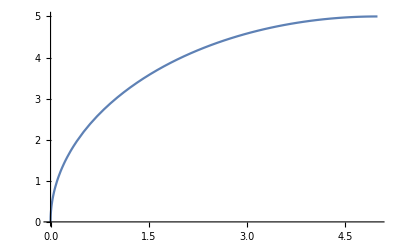

```mathematica
Plot[Sqrt[R^2-(x-R)^2]-0/.R->5, {x, 0, 5}]
```